# Mathematical Analysis Exam 3

## May 1, 2025. As always, and actually, on any exam from any professor, if you get bogged down on a problem, move on and come back later.

## Chapter 9 — Derivatives

Here is the definition of the derivative, which I didn’t ask you to memorize, but I hope you have:
-Graphics-

### 1. Application of the Definition of the Derivative

Obtain, working directly from the definition, the value of f'(a) for the function f(x)=1/x^2. In your derivation, you may use any property of limits that we obtained prior to Chapter 9.

(The point is not to reprove things we already proved. The point is to apply the arsenal of facts developed in Chapters 1-8 to make a new result easy.)

## Chapter 10 — Differentiation

### 2. Application of Differentiation Rules

Find f'(x) for each of the two following functions f. Don’t worry about the domain of f or f' if they have some points where they are ill-defined. The goal is not proofs. The goal is to accurately apply sum rule, product rule, quotient rule, and chain rule.

(a) f(x)=(sin(cos^2 x))/x

(b) f(x)=sin(x^2+sin x^2)

### 3. Obtain a Fancy Quotient Rule

Let A, B, C, D be four functions. Let f=(A·B)/(C·D).

NB: Those are times signs not composition of function symbols between A and B and between C and D.

By application of the quotient rule, and then by two applications of the product rule, get a pleasingly symmetrical expression for f'. By “pleasingly symmetrical,” I mean there should be four terms over a common denominator, and it should be clear that the exchanges, A<->B and C<->D, which clearly do not affect f, also do not affect f'.

## Chapter 11 — The Significance of the Derivative

## On the last page is a piece of graph paper. Use it for Problem 4 by separating it from the exam and turning it in with your work.

### 4. Using Derivatives to Aid Graphing

Consider the function f(x)=x+4/x^2.

(a) By taking a derivative, setting it equal to zero, and solving, you will find a value of x where f'(x)=0.

(b) Now that you have found that value of x, what is f(x) at that value?

(c) 4/x^2 becomes negligible when x is huge and positive (or huge and negative). If we could neglect  4/x^2 completely, we would just have the function f(x)=x. Of course we can’t neglect  4/x^2 completely. Use a ruler to draw the function f(x)=x with dashed lines on a piece of graph paper. The lines going off to plus and minus infinity you have drawn are called “asymptotes.”

(d) Add the point you found in (a) and (b) to the graph. Lightly draw a horizontal line through the point to indicate that this is the one place where the slope of f(x) is 0.

(e) Using what you learned in (a)-(d), crudely sketch the full function  f(x)=x+4/x^2 with solid lines. Your solid lines will approach but never touch the asymptotes as x->∞ or x->-∞. By “crudely,” I mean, you could just plug in two more easy values like x=1 and x=-1, and do the rest completely freehand.

### 5. A Simple Optimization Problem

The trajectory of a particle undergoing parabolic motion with no drag is:

Horizontal component of motion:           x(t)=v_0 t cosθ

Vertical component of motion:                 y(t)=v_0 t sinθ-1/2 g t^2

In these equations v_0 and g are positive constants (the muzzle velocity and the acceleration of gravity). The time t is the variable. For the moment θ is just another constant.

(a) Take y'(t), set it to 0, and use this to find the time of maximum height.

(b) Double the time you found in (a). Because it takes as long to reach maximum height as to come back to the ground, by doubling the time, you have found the time of impact. Now put the time of impact into the formula for the horizontal motion.

(c) Tidy up your answer to (b) using the double-angle formula, sin2θ=2sinθ cosθ.

(c) You found the formula for the distance to impact in (c). This is called the “range.” Your formula should no longer involve the time, t. Now think of θ as the variable and take the derivative of the range R(θ) with respect to θ, and set that to 0. That will tell you what angle θ gives the maximum range. What is the optimal angle?

COMMENT: If there is drag, the optimal angle is lower. -Graphics-

## Chapter 12 — Inverse Functions

Here is our favorite theorem (Theorem 5) from the inverse functions chapter:

-Graphics-

### 6. Leibniz Notation for Theorem 5

(a) Do what Spivak asks in Problem 17 of Chapter 12, which is simply to rewrite the result of Theorem 5, which without clutter is

             f^(-1 ')=1/f'
             
    in Leibniz notation. Here is the way Spivak asked it:

-Graphics-

I hope you left the arguments — which would be read aloud as “dx/dy at y” and “dy/dx at f^-1(y)” — out of your answer. You can leave the clutter out in Leibniz notation because it is generally understood in Leibniz notation that dx/dy is evaluated at y, that dy/dx is evaluated at x, and that x=f^-1(y).

NOTE: What you got is the sort of thing that people that love Leibniz notation do as if it were dx and dy were “infinitesimal” numbers which can be divided like ordinary numbers. If you imagine that dx and dy are separately meaningful things — which they aren’t — then the result even looks obvious.

(b) As an application of what you just found, for the function y=x^n, what is dy/dx? 

(c) Since the inverse function is x=y^(1/n), we can write dx/dy=(d y^(1/n))/dy. Use that to rewrite the left-hand-side of what you got in (a). Also use  the result you got in (b) in the denominator of the right-hand side.

(d) As a cross-check, make one final step. Put back that x=y^(1/n) in the denominator and simplify the powers. If you simplify correctly, you will recognize something familiar.

## Chapter 13 — Integrals

### 7. A Standard Integral

If you do the integral of x^2 from 0 to b, the answer is b^3/3. Let’s do a few steps of the proof of that following along with what Spivak did for the function x from 0 to b on pp. 258-9. Since there are 8 problems on this exam, and I am trying to keep them all short, I am going to do the first few steps for you:

If you partition the region from 0 to b into n equal parts, each has width b/n and the lower sum is:

L(f,n)=∑_(i=0)^(n-1) (ib/n)^2 b/n=∑_(i=1)^(n-1) (ib/n)^2 b/n.

In the second equality, I used that the i=0 term contributed nothing.

Meanwhile, the upper sum is:

U(f,n)=∑_(i=0)^(n-1) (((i+1)b)/n)^2 b/n=∑_(i=1)^n (ib/n)^2 b/n.

(a) Scrutinizing the work I did above, what is a pleasantly simple expression for the difference:

U(f,n)-L(f,n)

(b) The upper sum always approaches the value of the integral from above, and the lower sum always approaches it from below. To finish following what Spivak did on pp. 258-9, we want to “squeeze” the value of the integral from either side, and thereby show that the integral exists. To make the difference you found in (a) less than ϵ, how must we choose n as a function of b and ϵ?

## Chapter 14 — The Fundamental Theorem of Calculus

### 8. Two Applications of the (The First) Fundamental Theorem of Calculus

(a) Find a function g(x) that satisfies:

∫_0^x t g(t)dt=x+x^2

(b) Repeat, but for the slightly trickier problem:

∫_0^(x^2) t g(t)dt=x+x^2

## NAME: _____________________________

## 1 /3 2 /3 3 /3 4 /3 5 /4 6 /4 7 /2 8 /3 ============= TOTAL / 25

## Graph Paper for Problem 4.

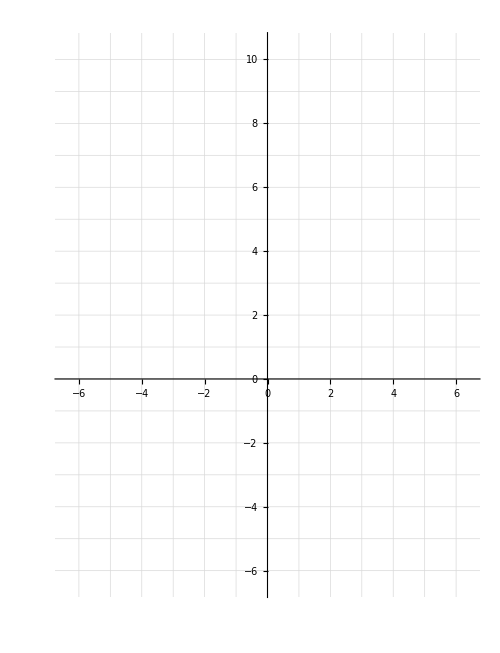

```mathematica
Plot[{},{x,-6.5,6.5},PlotRange->{{-6.5,6.5},{-6.5,10.5}},AspectRatio->17/13,Frame->False,GridLines->{Range[-6,6,1], Range[-6,10,1]},GridLinesStyle->Medium,AxesStyle->Thick]
```